## Task 4 _ 2

## Variant 3

```mathematica
stE = NDSolve[{y''[t]+0.2*y'[t]+y[t]*y[t]*y[t]+y[t]== Sin[t], y[0] == 1, y'[0] == 0}, y[t], {t, 0, 4*π}]
```

{{y[t]→InterpolatingFunction[{{0., 12.5664}}, <>][t]}}

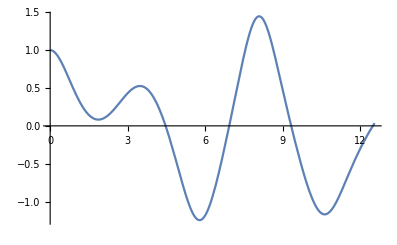

```mathematica
standartEPlot = Plot[Evaluate[y[t]/.stE],{t,0, 4*π},PlotRange->All]
```

```mathematica
euler[h_, a_, b_]:=(
ptr = a;
y0 = 1;
z0 = 0;
yList = {y0};
While[ptr ≤  b,
y1 = y0 + h*z0;
AppendTo[yList, y1];
z1 = z0+h(-0.2z0-y0-(y0*y0*y0)+Sin[ptr]);
z0 = z1;
y0 = y1;
ptr+=h;
];
yList
);
```

```mathematica
euler[0.1,0, 4*π]
```

{1,1.,0.98,0.941398,0.886343,0.817588,0.738275,0.651702,0.5611,0.469467,0.379463,0.293362,0.213058,0.140086,0.0756657,0.0207415,-0.0239907,-0.0580609,-0.0812138,-0.0934045,-0.0947954,-0.0857533,-0.0668426,-0.0388142,-0.00258995,0.0407556,0.0900147,0.143865,0.200886,0.259572,0.318344,0.375563,0.429542,0.478573,0.520951,0.555022,0.579233,0.592192,0.592731,0.579962,0.55332,0.512583,0.457865,0.389587,0.308419,0.215226,0.111004,-0.00316148,-0.126104,-0.256556,-0.393079,-0.533961,-0.677077,-0.819727,-0.958484,-1.08908,-1.20641,-1.30463,-1.37758,-1.41933,-1.42497,-1.39145,-1.31821,-1.2074,-1.06355,-0.892732,-0.701501,-0.495902,-0.280832,-0.0598358,0.164711,0.391152,0.617942,0.842976,1.06291,1.27252,1.4643,1.62828,1.75263,1.82492,1.83438,1.77462,1.64588,1.45578,1.21784,0.948278,0.662408,0.37223,0.085669,-0.192769,-0.460652,-0.716168,-0.956868,-1.17873,-1.37559,-1.53911,-1.65933,-1.72604,-1.73088,-1.66965,-1.54416,-1.3625,-1.13766,-0.884647,-0.617592,-0.347785,-0.0831207,0.171352,0.412344,0.637186,0.842897,1.02558,1.18019,1.30073,1.38081,1.41475,1.39867,1.3317,1.21649,1.05904,0.867624,0.651391,0.418909,0.177303,-0.0679774,-0.312813,-0.553726}

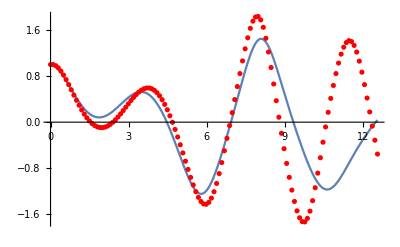

```mathematica
Show[standartEPlot, ListPlot[euler[0.1, 0, 4π],DataRange->{0,4π}, PlotStyle->Red]]
```

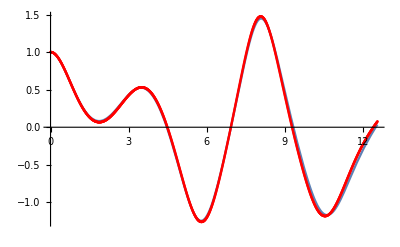

```mathematica
Show[standartEPlot, ListPlot[euler[0.01, 0, 4π],DataRange->{0,4π}, PlotStyle->Red]]
```

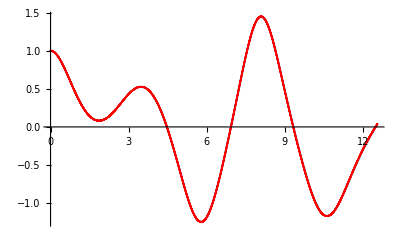

```mathematica
Show[standartEPlot, ListPlot[euler[0.001, 0, 4π],DataRange->{0,4π}, PlotStyle->Red]]
```